```mathematica
(*Author: HKUST,Robotics Institute, William Wu, Wenchao DING*)
(* Key idea of solving the max-min problem:
First, we solve the inner problem by deriving the closed-form solution of \Delta_r 
(dr in the script, i.e., the inflation we need) such that the two inflated balls 
 exactly cover the convex hull of the two original balls. 
This step can be done by expressing the geometry relationship and use the $Solve$ 
 function in mathematica. 

Afterwards, we solve the outer problem using the aforementioned 
 closed- form expression. It then becomes a pure maximization proble which can 
 be solved using $Maximize$ function in mathematica. Alternatively, we can 
 check the second order derivative and first order derivative to verify that the 
\Delta_r is monotonically decreasing with respect to delta (difference between the 
radius of the two balls, corresponds to \alpha in the paper). 

Note that the closed-form solution of \Delta_r contains two symmetric cases 
 after solving the equations induced by geometry relationship. And for each case,  
   depending on the interval of delta, the expression have two forms but can be assembled together. 
 After assembling the solutions for all valid intervals,  the resulting solution of \Delta_r is 
  continue everywhere. We also provide the suplementary results for checking the continuity. 
 *)

(* A visualization tool for problem description*)
Manipulate[
r1 = d/2-δ+df;
r2 = d/2 +δ+df;
c0=Circle[{0,0},r1];
c1 = Circle[{d,0},r2]; 
rc0 = Circle[{0,0},r1+dr];
rc1 = Circle[{d,0},r2+dr];
θ = ArcSin[(r2-r1)/d];
p0 = {-r1 Sin[θ],r1 Cos[θ]};
p1 = {d-r2 Sin[θ],r2 Cos[θ]};
p2 = {-r1 Sin[θ],-r1 Cos[θ]};
p3 = {d-r2 Sin[θ],-r2 Cos[θ]};
ans = Solve[{x,y}∈c1&&{x,y}∈c0,{x,y}];
ans2 = Solve[{x,y}∈rc1&&{x,y}∈rc0,{x,y}];{
Solve[{x,y}∈rc1&&{x,y}∈rc0&&({x,y}∈InfiniteLine[{p0,p1}]||{x,y}∈InfiniteLine[{p2,p3}]),dr],
Graphics[{{Green,InfiniteLine[{p0,p1}],InfiniteLine[{p2,p3}]},{Blue,c0,c1,rc0,rc1},{Red,PointSize[0.01],Point[{x,y}]/.ans,Point[{x,y}]/.ans2}}]/.{d->cd,δ->cδ,df->cdf,dr->cdr},{Red,rc0,rc1}},
{cd,1,10},{cδ,0.0001,cd/2},{cdf,0.01,10},{cdr,0.01,3}
]
```

```mathematica
(* Main program starts here. It may need a long time to output results. Just wait for some time *)
```

```mathematica
r1 = d/2-δ+df;
r2 = d/2 +δ+df;
c0=Circle[{0,0},r1];
c1 = Circle[{d,0},r2];
rc0 = Circle[{0,0},r1+dr];
rc1 = Circle[{d,0},r2+dr];
θ = ArcSin[(r2-r1)/d];
p0 = {-r1 Sin[θ],r1 Cos[θ]}
p1 = {d-r2 Sin[θ],r2 Cos[θ]}
p2 = {-r1 Sin[θ],-r1 Cos[θ]}
p3 = {d-r2 Sin[θ],-r2 Cos[θ]}
ans = Solve[d>0&&δ>0&&df>0&&{x,y}∈c1&&{x,y}∈c0,{x,y}];
ans2 = Solve[d>0&&δ>0&&df>0&&{x,y}∈rc1&&{x,y}∈rc0,{x,y}];
comment = Solve[d>0&&δ>0&&df>0&&{x,y}∈rc1&&{x,y}∈rc0&&({x,y}∈Line[{p0,p1}]||{x,y}∈Line[{p2,p3}]),{x,y,dr}];
(* *)
```

{(2 δ (-d/2-df+δ))/d,(d/2+df-δ) √(1-(4 δ^2)/d^2)}

{d-(2 δ (d/2+df+δ))/d,(d/2+df+δ) √(1-(4 δ^2)/d^2)}

{(2 δ (-d/2-df+δ))/d,(-d/2-df+δ) √(1-(4 δ^2)/d^2)}

{d-(2 δ (d/2+df+δ))/d,(-d/2-df-δ) √(1-(4 δ^2)/d^2)}

```mathematica
comment⟦1⟧(*first answer of the closed form solution of [x,y] position and dr (Delta_r) click shift+enter to see the detailed solution*)
```

```mathematica
comment⟦2⟧(*second answer of the closed form solution of [x,y] position and dr (Delta_r), click shift+enter to see the detailed solution*)
```

```mathematica
comment⟦3⟧(*third answer of the closed form solution of  [x,y] position and dr (Delta_r), click shift+enter to see the detailed solution*)
```

```mathematica
comment⟦4⟧(*fourth answer of the closed form solution of [x,y] position and dr (Delta_r), click shift+enter to see the detailed solution*)
```

```mathematica
(*
 we represent \Delta_r w.r.t d, \delta and df. Here we use
a fixed d = 2. And also we make use of the observation that the extrema only occurs at df = 0. As such we limit d_f
to a very small value in the visualizaton. *)
```

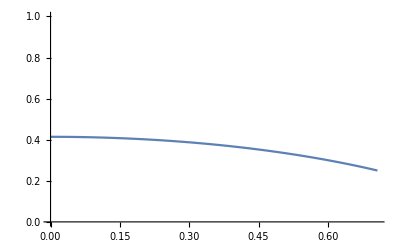
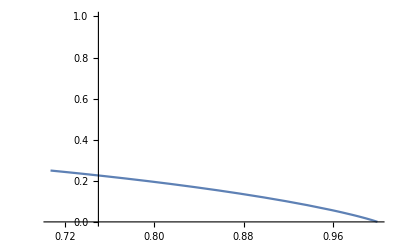
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pdr = dr/.comment;
(* We plot \Delta_r with respect to \delta for visualization.*)
Plot[#,{δ,0.00001,1},PlotRange->{0,1}]&/@(pdr/.{d->2,df->0.00000001})
```

```mathematica
(*The assembled results of \Delta_r w.r.t \delta can be got via combining plot 1 and plot 3 (plot 2 and plot 4 are the other symmetric case). There are four plots but actually only two cases which are symmetric
In the plot, we can find that when \delta->0, the maximum \Delta_r can be found. *)
```

```mathematica
(*Here we solve the outer maximization problem in the rectangle range explicitly. Note that for delta->0, we have 
  some numerical issue, since the two intersections points used in the formulation are reducing to one. For this extreme case,
   we check the limit and make sure that the function is actually continue at this point (not unbounded) *)
```

```mathematica
Maximize[{#,δ<df,δ<0.7}/.d->2,{δ,df}∈Rectangle[{0.00001,0.00001},{1,1}]]&/@Take[pdr,2]
```

{{0.414211,{δ→0.00001,df→0.00001}},{0.414211,{δ→0.00001,df→0.00001}}}

```mathematica
(*   We check the continuity at \delta = 0 to make sure there is no invalid extrema.  
  Specifically, for \delta = 0, we can easility get \Delta_r = (sqrt(2) - 1)/2 * d. 
  On the other hand, for \delta -> 0+, we can use the following to calculate the limit. 
  (\delta -> 0+ and \delta -> 0- are two symmetric cases, and the limits are the same.) 
     Therefore, for function \Delta_r = f(delta), it is continue at delta = 0 *)
```

```mathematica
Limit[#/.d->2,δ->0]&/@Take[pdr,2]
```

{ConditionalExpression[-1-df+√(2+2 df+df^2),df>0],ConditionalExpression[-1-df+√(2+2 df+df^2),df>0]}